Problem 7.8

```mathematica
(*Use DSolve to get the solution to the differential equation*)
```

```mathematica
DSolve[x^2*f''[x]+x*f'[x]+(x^2-n^2)*f[x]==0,f[x],x]
```

{{f[x]→BesselJ[n,x] C[1]+BesselY[n,x] C[2]}}

```mathematica
%[[1]]
```

{f[x]→BesselJ[n,x] C[1]+BesselY[n,x] C[2]}

```mathematica
%[[1]]
```

f[x]→BesselJ[n,x] C[1]+BesselY[n,x] C[2]

```mathematica
(*Use the % to get the actual answer inside the solution array*)
```

```mathematica
DSolve[(1-x^2)*f''[x]-2*x*f'[x]+n*(n+1)*f[x]==0,f[x],x]
```

{{f[x]→C[1] LegendreP[n,x]+C[2] LegendreQ[n,x]}}

```mathematica
(*Now we'll use DSolve to solve the next differential equation*)
```

```mathematica
%[[1]]
```

{f[x]→C[1] LegendreP[n,x]+C[2] LegendreQ[n,x]}

```mathematica
%[[1]]
```

f[x]→C[1] LegendreP[n,x]+C[2] LegendreQ[n,x]

```mathematica
(*Use the % to get the actual answer inside the solution array*)
```

Problem 7.9

```mathematica
(*Note that a symbolic solution does not work for this differential equation*)
```

```mathematica
DSolve[y''[x]==10*Sin[y[x]]*Cos[x],y[x],x]
```

DSolve[y''[x]==10 Cos[x] Sin[y[x]],y[x],x]

```mathematica
(*We have to write it as two first order equations*)
```

```mathematica
eqns = {y'[x]==v[x],v'[x]==10*Sin[y[x]]*Cos[x],v[0]==0.1,y[0]==0}
```

{y'[x]==v[x],v'[x]==10 Cos[x] Sin[y[x]],v[0]==0.1,y[0]==0}

```mathematica
(*Define xmin and xmax and then solve the differential equation with the two first order ones*)
```

```mathematica
xmin=0;xmax=100;
nsols=NDSolve[eqns,{y[x],v[x]},{x,xmin,xmax}]
```

{{y[x]→InterpolatingFunction[…][x],v[x]→InterpolatingFunction[…][x]}}

```mathematica
(*Plot y and v with the appropriate interval of x*)
```

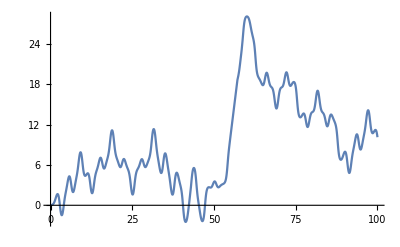

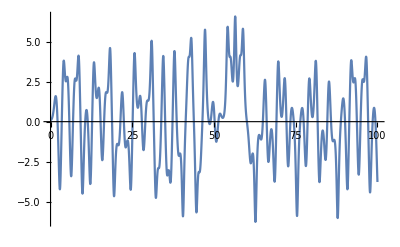

```mathematica
position= y[x]/.nsols[[1]];
velocity =v[x]/.nsols[[1]];
Plot[position,{x,0,100}]
Plot[ velocity,{x,0,100}]
```